```mathematica
ClearAll/@{ϕ,pointGen,trigApproximation,getResultY,test};
ϕ[x_,k_]:=If[k==1,1,Sin[(k-1)*x]]
pointGen[f_,n_,left_,right_]:={Table[N@left+(i(right-left))/(n-1),{i,0,n-1}],Table[f[N@left+(i(right-left))/(n-1)],{i,0,n-1}]}
trigApproximation[points_, n_]:=Module[
{matrix,coef, N,x,f,res},
x=points[[1]];
f=points[[2]];
N=Length@x;
matrix=Table[Sum[ϕ[x[[j]],i]ϕ[x[[j]],k],{j,N}],{i,n},{k,n}];
coef=Table[Sum[ϕ[x[[j]],i]f[[j]],{j,N}],{i,n}];
Print@coef;
res=LinearSolve[matrix,coef];
res
]
getResultY[ax_,x_]:=Sum[ax[[i]]ϕ[x,i],{i,Length@ax}];

test[f_,n_,l_,r_]:=Module[
{coef,N=1000, e=0.5,p},
p=pointGen[f,N,l,r];
coef=trigApproximation[p,n];
Show[
Plot[f[x],{x,l,r}],
(*ListPlot[Transpose@p,PlotStyle->Red],*)
Plot[getResultY[coef,x],{x,l,r},PlotStyle->Orange]
]
]
```

```mathematica
ClearAll@f1;
ClearAll@f2;
error[n_]:=RandomReal[{-n,n}]
f1[x_]:=Sin[2x]+x^2/10-x+1+error[0.5]
f2[x_]:=E^-x+(3x)/(x^2+1)+x+error[0.3]
```

{1132.,-632.241,213.378,598.031}

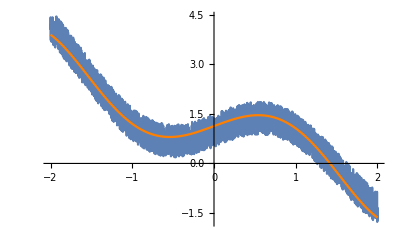

{3299.76,1153.26,393.085,-205.568,352.833,-34.706,-48.5975}

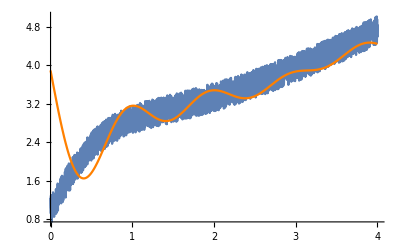

```mathematica
test[f1,4,-2,2]
test[f2,7,0,4]
```